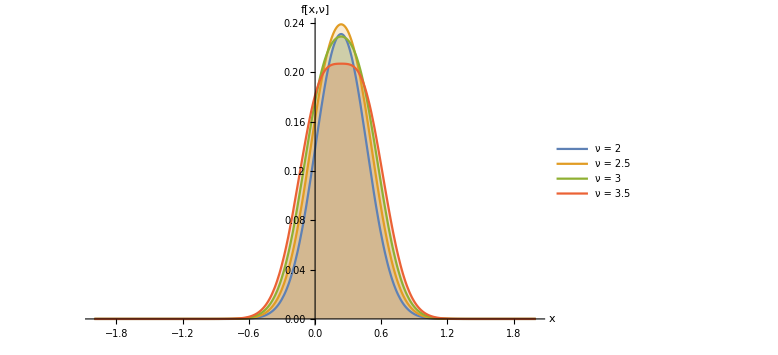

```mathematica
a=Plot[Table[PDF[ChiSquareDistribution[ν],2.5754552237209665-8.737856713302271 x+18.500684807545397 x^2],{ν,{2,2.5,3,3.5}}]//Evaluate,{x,-2,2},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 2","ν = 2.5","ν = 3","ν = 3.5"},FrameLabel->{{None,None},{None,HoldForm[χ^2]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Gm poly pdf.png",a]
```

Gm poly pdf.png

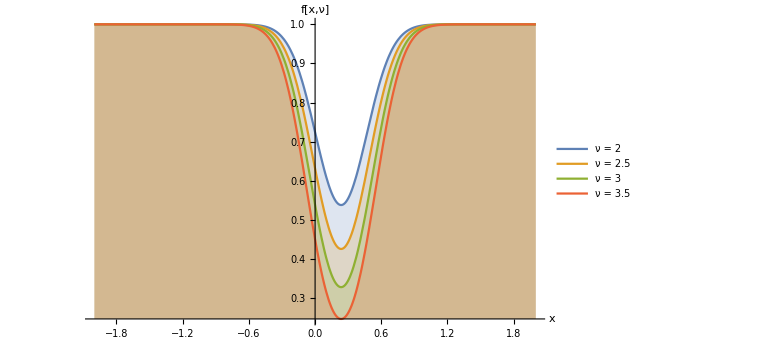

```mathematica
b=Plot[Table[CDF[ChiSquareDistribution[ν],2.5754552237209665-8.737856713302271 x+18.500684807545397 x^2],{ν,{2,2.5,3,3.5}}]//Evaluate,{x,-2,2},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 2","ν = 2.5","ν = 3","ν = 3.5"},FrameLabel->{{None,None},{None,HoldForm[χ^2]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Gm poly cdf.png",b]
```

Gm poly cdf.png

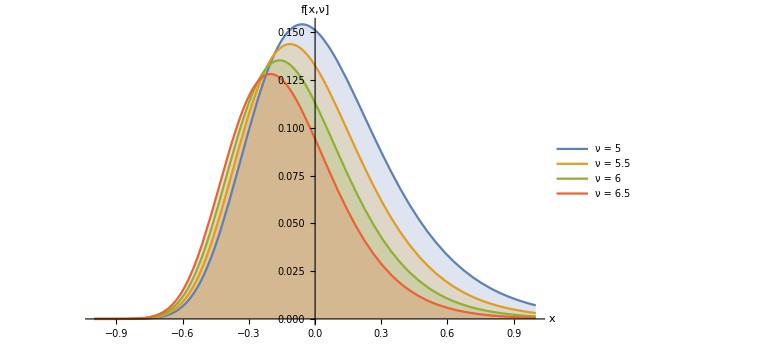

```mathematica
c=Plot[Table[PDF[ChiSquareDistribution[ν],2.5369781307297643 ⅇ^(-2.8332539983226597 t)],{ν,{5,5.5,6,6.5}}]//Evaluate,{t,-1,1},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 5","ν = 5.5","ν = 6","ν = 6.5"},FrameLabel->{{None,None},{None,HoldForm[χ^2]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Gm exp pdf.png",c]
```

Gm exp pdf.png

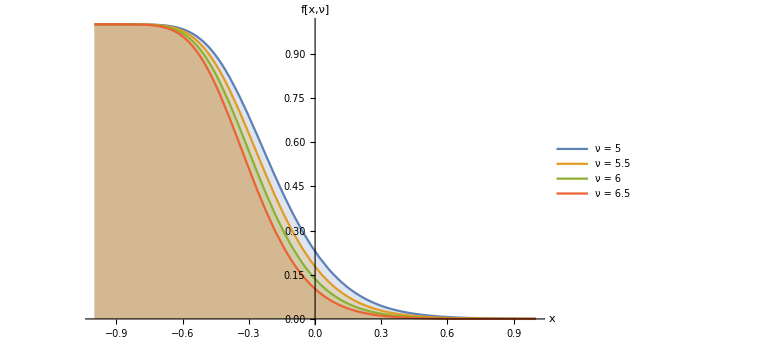

```mathematica
d=Plot[Table[CDF[ChiSquareDistribution[ν],2.5369781307297643 ⅇ^(-2.8332539983226597 t)],{ν,{5,5.5,6,6.5}}]//Evaluate,{t,-1,1},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 5","ν = 5.5","ν = 6","ν = 6.5"},FrameLabel->{{None,None},{None,HoldForm[χ^2]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Gm exp cdf.png",d]
```

Gm exp cdf.png